```mathematica
Qfield[x_]:=(({{0, -1}, {1, 0}}).x)/(2π Max[x.x,0.001])
Mfield[x_]:=(*x/(x.x eps)Exp[-(√(x.x))/eps]*)If[x=={0,0},0,x/(x.x eps)Exp[-(√(x.x))/eps]]
```

```mathematica
Условия задачи
```

```mathematica
ν=(*1/1000*)10^-4;τ=0.1;eps=0.0001;Vinf={1,0};KMax=20;ρ=1;
```

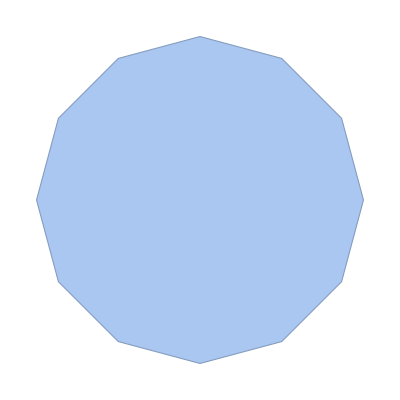

```mathematica
Rdots=Table[{Cos[t],Sin[t]},{t,-Pi/2,3Pi/2-0.01,Pi/6}];
Rarea=BoundaryMeshRegion[Rdots,Line[Append[Range[1,Length@Rdots],1]]]
```

```mathematica
Rmids=(RotateLeft@Rdots+Rdots)/2;
Rsides=(RotateLeft@Rdots-Rdots);
rotRsides=RotateLeft@Rsides;
lSides=Table[N@√(Rsides[[i]].Rsides[[i]]),{i,Length@Rsides}];
minimalSide=Min@lSides;
```

```mathematica
Rnormals=Transpose@(({{0, -1}, {1, 0}}).Transpose@Rsides);
```

```mathematica
Rnormals=Table[Rnormals[[i]]/(√(Rnormals[[i]].Rnormals[[i]])),{i,Length@Rnormals}];
```

```mathematica
curlDeploy=1.05Rdots;
activeDeploys=Take[curlDeploy,7];
passiveDeploys=Take[curlDeploy,{8,Length@curlDeploy}];
```

```mathematica
pics={};pics2={};
```

```mathematica
Предварительное составление матрицы и нахождение начальных вихрей
```

```mathematica
L1=Table[Qfield[Rmids[[i]]-curlDeploy[[j]]].Rnormals[[i]],{i,1,Length@Rdots},{j,1,Length@Rdots}];
newGamma=Table[{G[i]},{i,1,Length@Rdots}];
f0=N@Rnormals.Vinf;
curlsOnPanel={};
curlsInFlow={};

Force={};
Momentum={};


solution=Solve[{L1.newGamma+r==-f0,Sum[newGamma[[i]],{i,Length@newGamma}]==0},Append[First@Transpose@newGamma,r]];
nGammaR=Append[First@Transpose@newGamma,r]/.First@solution;

curlsInFlow=Table[{nGammaR[[i]],activeDeploys[[i]]},{i,Length@activeDeploys}];
curlsOnPanel=Table[{nGammaR[[i]],passiveDeploys[[i-Length@activeDeploys]]},{i,Length@activeDeploys+1,Length@curlDeploy}];

(*For[i=1,i≤Length@nGammaR-1,i++,AppendTo[curlsOnPanel,{nGammaR[[i]],curlDeploy[[i]]}]];*)
minCurl=Max[Abs@nGammaR]*0.001;
```

```mathematica
AllCurls=Join[curlsInFlow,curlsOnPanel];
Vfield=Vinf+Sum[First@AllCurls[[i]]Qfield[{x,y}-Last@AllCurls[[i]]],{i,Length@AllCurls}];
```

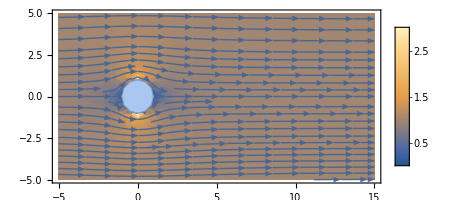

```mathematica
Show[DensityPlot[√(Vfield.Vfield),{x,-5,15},{y,-5,5},PlotLegends->Automatic,PlotRange->{-1,3}],StreamPlot[Vfield,{x,-5,15},{y,-5,5},StreamPoints->Fine],Rarea,AspectRatio->1/2]
```

```mathematica
L2=Append[Table[Append[L1[[i]],1],{i,1,Length@L1}],Append[Table[1,{j,1,Length@L1}],0]];
invL2=Inverse@L2;
```

```mathematica
For[k=0,k<KMax,k++,
(*  "рождение" новых вихрей в curlDeploy  *)

(*AllCurls=Join[curlsInFlow,curlsOnPanel];*)
f1=Table[Sum[Rnormals[[i]].Qfield[Rmids[[i]]-Last@curlsInFlow[[m]]]First@curlsInFlow[[m]],{m,1,Length@curlsInFlow}],{i,1,Length@curlDeploy}];
nGammaR=-invL2.(Append[f0+f1,0]);

curlsInFlow=Join[curlsInFlow,Table[{nGammaR[[i]],activeDeploys[[i]]},{i,Length@activeDeploys}]];
curlsOnPanel=Table[{nGammaR[[i]],passiveDeploys[[i-Length@activeDeploys]]},{i,Length@activeDeploys+1,Length@curlDeploy}];

AllCurls=Join[curlsInFlow,curlsOnPanel];
(*valueAllCurls=Table[AllCurls[[i]],{i,Length@AllCurls}];*)
etaR=Table[{x,y}-Rmids[[i]],{i,Length@Rmids}]/eps;
modEtaR=Table[etaR[[i]].etaR[[i]],{i,Length@Rmids}];
primeR=Table[{x,y}-Last@AllCurls[[i]],{i,Length@AllCurls}];
modPrimeR=Table[primeR[[i]].primeR[[i]],{i,Length@AllCurls}];

I3=-Sum[Rnormals[[i]]Exp[-√modEtaR[[i]]],{i,Length@Rnormals}];I0=2π eps^2+eps Sum[(etaR[[i]].Rnormals[[i]])/modEtaR[[i]](√modEtaR[[i]]+1)Exp[-√modEtaR[[i]]]lSides[[i]],{i,Length@Rnormals}];

curlsInFlow=ParallelTable[{First@curlsInFlow[[i]],Last@(curlsInFlow[[i]])+τ (Vfield+(ν I3)/I0)/.{x->First@Last@(curlsInFlow[[i]])(*+eps/1000*),y->Last@Last@(curlsInFlow[[i]])(*+eps/1000*)}}
-τ ν (Sum[Mfield[Last@curlsInFlow[[i]]-Last@AllCurls[[j]]]First@AllCurls[[j]],{j,Length@AllCurls}])/Sum[First@AllCurls[[j]]Exp[-√((Last@curlsInFlow[[i]]-Last@(AllCurls[[j]])).(Last@curlsInFlow[[i]]-Last@(AllCurls[[j]])))/eps],{j,1,Length@AllCurls}],{i,Length@curlsInFlow}];

For[i=1,i≤Length@curlsOnPanel,i++,If[RegionMember[Rarea,Last@(curlsOnPanel[[i]])] ||Abs@ First@(curlsOnPanel[[i]])<minCurl,curlsOnPanel[[i]][[2]]=curlDeploy[[i]];curlsOnPanel[[i]][[1]]=nGammaR[[i]];];];
(*curlsOnPanel=Delete[curlsOnPanel,curlsToRemove];*)
curlsToRemove={};
For[i=1,i≤Length@curlsInFlow,i++,If[RegionMember[Rarea,Last@(curlsInFlow[[i]])] ||Abs@ First@(curlsInFlow[[i]])<minCurl,AppendTo[curlsToRemove,{i}]];];
curlsInFlow=Delete[curlsInFlow,curlsToRemove];
AllCurls=Join[curlsInFlow,curlsOnPanel];
Vfield=Vinf+Sum[First@AllCurls[[i]]Qfield[{x,y}-Last@AllCurls[[i]]],{i,Length@AllCurls}];

AppendTo[Force, ρ (Sum[nGammaR[[i]]/τ ({{0, -1}, {1, 0}}).Rmids[[i]],{i,Length@Rmids}]
+ν Sum[First@AllCurls[[i]] ({{0, -1}, {1, 0}}).Rnormals[[j]](Exp[-√modEtaR[[j]]]/2π eps^2(*I0*)/.{x->First@Rmids[[j]],y->Last@Rmids[[j]]})lSides[[j]],{i,Length@AllCurls},{j,Length@Rmids}]   )];

(*If[Mod[k,5]==0,
AppendTo[pics2,Show[(*ContourPlot[Vfield.Vfield,{x,-2,4},{y,-2,2},PlotLegends->Automatic,PlotRange->{-1,3}],*)StreamPlot[Vfield,{x,-5,15},{y,-5,5}(*,Mesh->5*)],Rarea,AspectRatio->1/2]];
CurlsGraph=Table[Graphics[{White,Disk[Last@AllCurls[[i]],1/20]}],{i,Length@AllCurls}];
AppendTo[pics,Show[ContourPlot[0,{x,-5,15},{y,-5,5}],Rarea,CurlsGraph,AspectRatio->1/2]];]*)
];//AbsoluteTiming
```

{160.499,Null}

```mathematica
ProgressIndicator[Dynamic[k/KMax]]
```

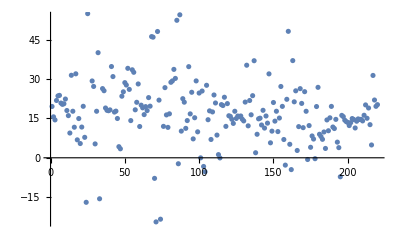
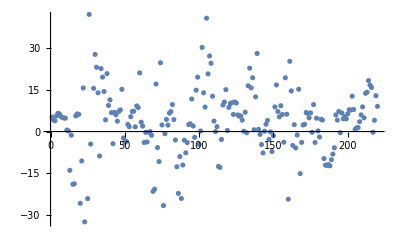

17.0307

3.66803

```mathematica
{ListPlot@First@Transpose@Force,ListPlot@Last@Transpose@Force}
Sum[(First@Transpose@Force)[[i]],{i,50,Length@Force}]/(Length@Force-50)
Sum[(Last@Transpose@Force)[[i]],{i,50,Length@Force}]/(Length@Force-50)
```

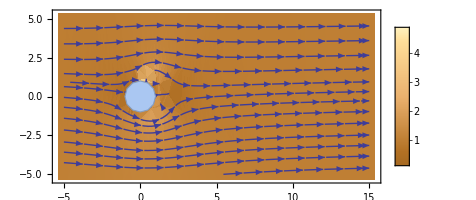

```mathematica
Show[StreamDensityPlot[Vfield,{x,-5,15},{y,-5,5},StreamPoints->Fine,PlotLegends->Automatic,StreamScale->{0.06,25},PerformanceGoal->"Speed"],Rarea,AspectRatio->1/2]
```

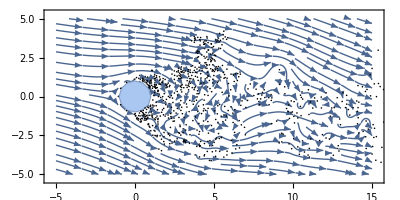

```mathematica
CurlsGraph=Table[Graphics[{Black,Disk[Last@AllCurls[[i]],1/20]}],{i,Length@AllCurls}];
Show[StreamPlot[Vfield,{x,-5,15},{y,-5,5},StreamPoints->Fine],Rarea,CurlsGraph,AspectRatio->1/2]
```

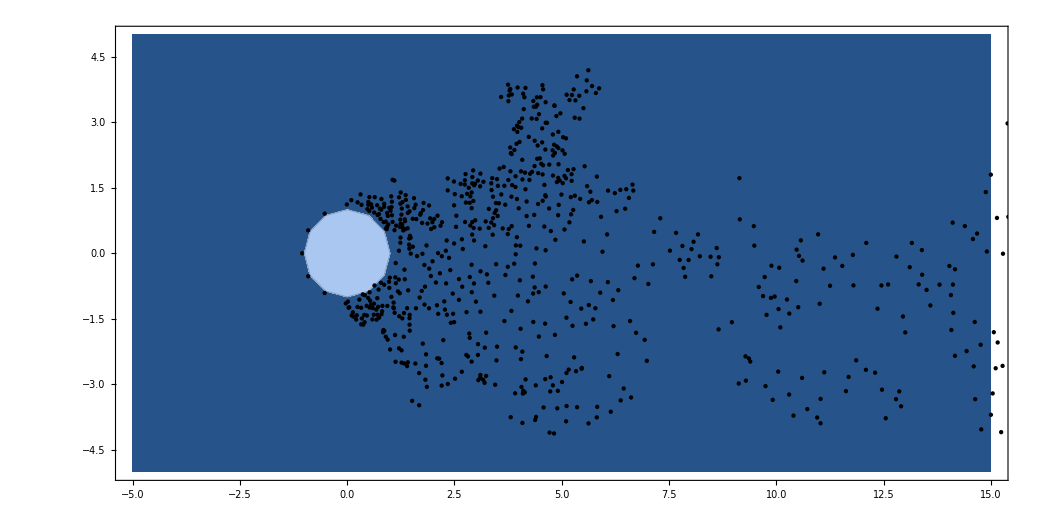

```mathematica
CurlsGraph=Table[Graphics[{Black,Disk[Last@AllCurls[[i]],1/20]}],{i,Length@AllCurls}];
Show[ContourPlot[0,{x,-5,15},{y,-5,5}],Rarea,CurlsGraph,AspectRatio->1/2]
```

```mathematica
Export["Cylinder_flow_bugged.gif",pics2]
```

Cylinder_flow_bugged.gif

```mathematica
Length@pics2
```

0

```mathematica
pics[[8]]
```

Part::partw: Part 8 of {} does not exist.

{}⟦8⟧